Connect to the NanoVNA

```mathematica
dev = DeviceOpen["Serial","/dev/ttyACM0"]
```

DeviceObject[…]

Copy code from cmd to make Reading more stable. readResponce keeps reading the buffer until there is no more information.

```mathematica
readPartial[front_]:=front<>FromCharacterCode[DeviceReadBuffer[dev]];
noPrompt[s_]:=!StringMatchQ[s,___~~"\r\nch> "~~EndOfString];
readResponse[]:=NestWhile[readPartial,"",noPrompt];
```

Function for Scanning. Takes the parameters and sends it to the Nano VNA. This function takes the starting HZ, the ending HZ, and the number of points in-between. After this data is sent to the NanoVNA, it is formatted by  removing everything before “data” for each port. The output of this function is then formatted into pairs of  {f,{x0,y0},{x1,y1}}.

```mathematica
runScan[startHZ_,endHZ_,points_] := (WriteString["/dev/ttyACM0",StringJoin[Riffle[{"scan",ToString[startHZ],ToString[endHZ],ToString[points]}," "]]<>"\r"];
Pause[2];
WriteString["/dev/ttyACM0","data 0"<>"\r"];
data1 =StringSplit[readResponse[]];
n = Position[data1,"data"];
datax = ToExpression[Take[Drop[data1,First[Flatten[n]]+1],points*2]];
Pause[1];
WriteString["/dev/ttyACM0","data 1"<>"\r"];
data2 = StringSplit[readResponse[]];
m = Position[data2,"data"];
datay = ToExpression[Take[Drop[data2,First[Flatten[m]]+1],points*2]];
f[n_] := ((endHZ - startHZ)/(points)n + startHZ);
frequencies = Array[
f
,points];

y[z_]:=
(result = {};
AppendTo[result,frequencies[[z]]]; 
AppendTo[result,datax[[2z-1;;2z]]];
AppendTo[result,datay[[2z-1;;2z]]];
Return[result]
);
final = Array[ y
,points]
 )
```

This is a test scan in order to check that everything is working. The parameters are [starting HZ, ending HZ, number of points ]. This test scan is stored as res in case it needs to be used later.

```mathematica
res =runScan[100000000,200000000,101]
```

{{10200000000/101,{0.458257,0.492512},{-7.113×10^-6,0.000040298}},{10300000000/101,{0.485951,0.448805},{9.202×10^-6,-0.000015264}},{10400000000/101,{0.509528,0.404183},{0.000022949,-0.000018421}},{10500000000/101,{0.529599,0.356514},{-6.563×10^-6,-0.000025101}},{10600000000/101,{0.546156,0.310149},{9.15×10^-7,-4.476×10^-6}},{10700000000/101,{0.557648,0.259779},{1.711×10^-6,0.000012061}},{10800000000/101,{0.567161,0.209556},{-3.38×10^-6,0.000011731}},{10900000000/101,{0.568207,0.157391},{2.456×10^-6,6.577×10^-6}},{11000000000/101,{0.564086,0.104651},{-0.00001087,0.000010184}},{11100000000/101,{0.549154,0.0580272},{-3.488×10^-6,-3.759×10^-6}},{11200000000/101,{0.532334,0.0216012},{-0.000028499,9.59×10^-6}},{11300000000/101,{0.523627,-0.00706824},{-0.00004233,0.000029666}},{11400000000/101,{0.522478,-0.043595},{-0.000030789,9.438×10^-6}},{11500000000/101,{0.517003,-0.0875637},{-0.000015441,0.000025255}},{11600000000/101,{0.503412,-0.134933},{-9.178×10^-6,0.000043297}},{11700000000/101,{0.483198,-0.180666},{9.486×10^-6,0.000037772}},{11800000000/101,{0.456921,-0.224366},{0.000019503,0.000051747}},{11900000000/101,{0.426215,-0.264753},{0.00002999,0.000020606}},{12000000000/101,{0.39124,-0.301621},{-9.194×10^-6,0.000026517}},{12100000000/101,{0.352928,-0.334713},{0.00003458,9.095×10^-6}},{12200000000/101,{0.311378,-0.363856},{0.000027642,0.000024319}},{12300000000/101,{0.267479,-0.388375},{0.000026425,1.309×10^-6}},{12400000000/101,{0.221491,-0.408491},{0.000012237,0.000017701}},{12500000000/101,{0.173969,-0.423984},{0.000027107,8.108×10^-6}},{12600000000/101,{0.125275,-0.434725},{0.000018719,-0.000011464}},{12700000000/101,{0.0760297,-0.440679},{1.648×10^-6,-0.000013311}},{12800000000/101,{0.0266128,-0.441792},{0.000010033,-7.733×10^-6}},{12900000000/101,{-0.0224445,-0.438195},{9.036×10^-6,8.29×10^-7}},{13000000000/101,{-0.0708458,-0.429878},{0.000037696,-0.000029005}},{13100000000/101,{-0.117959,-0.416849},{-0.000011391,-6.719×10^-6}},{13200000000/101,{-0.163432,-0.399449},{8.21×10^-7,-0.000030234}},{13300000000/101,{-0.206885,-0.377956},{-0.000041867,-0.000037633}},{13400000000/101,{-0.247901,-0.352313},{-0.000021144,-0.000043758}},{13500000000/101,{-0.285992,-0.323209},{-0.000026999,-0.000042678}},{13600000000/101,{-0.321093,-0.290634},{-0.000037811,-0.000068208}},{13700000000/101,{-0.352773,-0.255122},{-0.000038028,-0.00005543}},{13800000000/101,{-0.380798,-0.216772},{-0.000035178,-0.000064043}},{13900000000/101,{-0.405063,-0.176346},{-0.000030933,-0.000055176}},{14000000000/101,{-0.425231,-0.133929},{-0.000039545,-0.000061465}},{14100000000/101,{-0.441365,-0.0900725},{-0.00006009,-0.000042336}},{14200000000/101,{-0.453256,-0.045138},{-0.000046221,-0.000024403}},{14300000000/101,{-0.460972,0.00044142},{-0.000052768,-0.000033094}},{14400000000/101,{-0.464432,0.0460896},{-0.000058919,-0.000042901}},{14500000000/101,{-0.463967,0.0917566},{-0.000050655,-0.000042142}},{14600000000/101,{-0.45941,0.136954},{-0.000076089,-0.000047104}},{14700000000/101,{-0.451062,0.18147},{-0.000056452,-0.000030862}},{14800000000/101,{-0.438993,0.225001},{-0.000046614,-0.00004488}},{14900000000/101,{-0.423208,0.267127},{-0.000088121,-0.000040916}},{15000000000/101,{-0.404041,0.307572},{-0.000074581,-0.000026735}},{15100000000/101,{-0.381666,0.346226},{-0.00005917,-0.000051238}},{15200000000/101,{-0.356054,0.382617},{-0.0000877,-0.000032007}},{15300000000/101,{-0.327894,0.416826},{-0.000090468,-0.000039111}},{15400000000/101,{-0.296881,0.448381},{-0.000089657,-0.000012524}},{15500000000/101,{-0.263611,0.477566},{-0.000088784,-6.874×10^-6}},{15600000000/101,{-0.228132,0.503787},{-0.000111309,7.99×10^-7}},{15700000000/101,{-0.190873,0.527159},{-0.000080997,-0.000014996}},{15800000000/101,{-0.151821,0.547505},{-0.000073875,-3.212×10^-6}},{15900000000/101,{-0.111803,0.564827},{-0.000077992,-0.000019721}},{16000000000/101,{-0.0703486,0.579029},{-0.000083398,-3.526×10^-6}},{16100000000/101,{-0.0281261,0.589877},{-0.000077732,-0.000012039}},{16200000000/101,{0.0147342,0.597641},{-0.000077363,0.000018391}},{16300000000/101,{0.0577857,0.602416},{-0.000089628,0.000016045}},{16400000000/101,{0.101208,0.603819},{-0.000077762,0.000053151}},{16500000000/101,{0.144527,0.602245},{-0.0000822,0.000030602}},{16600000000/101,{0.187538,0.597744},{-0.00006126,0.000023365}},{16700000000/101,{0.230134,0.58988},{-0.000068809,0.000019599}},{16800000000/101,{0.271829,0.579195},{-0.000047085,0.000017725}},{16900000000/101,{0.312684,0.565702},{-0.000079372,0.000045973}},{17000000000/101,{0.352671,0.549337},{-0.000055064,0.000057007}},{17100000000/101,{0.39144,0.530056},{-0.000066939,0.000025269}},{17200000000/101,{0.428145,0.508289},{-0.000029018,0.000054057}},{17300000000/101,{0.463116,0.483773},{-0.000053426,0.000048384}},{17400000000/101,{0.496046,0.457293},{-0.000033299,0.000056073}},{17500000000/101,{0.527094,0.429409},{-0.000040741,0.000087783}},{17600000000/101,{0.55625,0.399724},{-4.35×10^-7,0.000071162}},{17700000000/101,{0.583603,0.368337},{2.768×10^-6,0.000073725}},{17800000000/101,{0.609176,0.335272},{-0.000010926,0.000072207}},{17900000000/101,{0.632479,0.300799},{0.000025861,0.000063282}},{18000000000/101,{0.653744,0.264894},{0.000012296,0.000076804}},{18100000000/101,{0.672536,0.227786},{0.000031749,0.00006977}},{18200000000/101,{0.689074,0.189575},{0.00002938,0.00008128}},{18300000000/101,{0.703648,0.15092},{-6.627×10^-6,0.000050997}},{18400000000/101,{0.71579,0.110916},{0.000017807,0.000019019}},{18500000000/101,{0.724909,0.0708307},{0.000020895,0.000051189}},{18600000000/101,{0.73187,0.0299341},{0.000017554,0.000045021}},{18700000000/101,{0.736375,-0.0110926},{5.044×10^-6,0.000044382}},{18800000000/101,{0.738366,-0.0521191},{0.000025525,0.000039428}},{18900000000/101,{0.738169,-0.0931698},{4.444×10^-6,0.000021511}},{19000000000/101,{0.735433,-0.134142},{0.000041857,0.000037156}},{19100000000/101,{0.730505,-0.174787},{0.00002961,0.000063036}},{19200000000/101,{0.723189,-0.214912},{0.000059876,0.000028481}},{19300000000/101,{0.713934,-0.254579},{0.000040607,0.000038144}},{19400000000/101,{0.702379,-0.293495},{0.000042925,0.000015081}},{19500000000/101,{0.688644,-0.331839},{0.000037422,0.000023217}},{19600000000/101,{0.672871,-0.369175},{0.000025979,0.000029369}},{19700000000/101,{0.655375,-0.406124},{0.00005261,0.000017518}},{19800000000/101,{0.635552,-0.441066},{0.000049894,0.000014926}},{19900000000/101,{0.614221,-0.475358},{0.000048299,0.000029468}},{20000000000/101,{0.590745,-0.508112},{0.000052845,0.000022316}},{20100000000/101,{0.566127,-0.539804},{0.000042899,0.000042437}},{200000000,{0.539804,-0.570137},{0.000049452,0.000011847}}}

Takes the parameters as raw data for troubleshooting. Data(n) is data from port n nanoVNA, data(var) is the processed data for each consecutive port

```mathematica
frequencies
```

```mathematica
data1
datax
data2
datay
```

{scan,100000000,200000000,101,ch>,data,0,0.458256608,0.492512032,0.485951200,0.448804576,0.509527872,0.404183200,0.529599424,0.356513568,0.546155712,0.310149056,0.557647680,0.259779488,0.567161408,0.209556112,0.568207232,0.157390528,0.564085888,0.104651104,0.549154048,0.058027188,0.532333664,0.021601208,0.523627168,-0.007068240,0.522477568,-0.043594952,0.517003104,-0.087563712,0.503412192,-0.134932704,0.483197536,-0.180665728,0.456921248,-0.224366048,0.426215456,-0.264752544,0.391240384,-0.301620800,0.352927808,-0.334712928,0.311378112,-0.363855776,0.267478608,-0.388375040,0.221491232,-0.408490752,0.173969168,-0.423984096,0.125274600,-0.434724896,0.076029744,-0.440678816,0.026612788,-0.441792320,-0.022444454,-0.438195136,-0.070845848,-0.429877728,-0.117958576,-0.416849056,-0.163431504,-0.399449216,-0.206885072,-0.377956032,-0.247901152,-0.352312640,-0.285992224,-0.323209440,-0.321093312,-0.290634240,-0.352773088,-0.255122000,-0.380797824,-0.216772288,-0.405063360,-0.176345808,-0.425231360,-0.133929264,-0.441365280,-0.090072472,-0.453255744,-0.045137976,-0.460971520,0.000441420,-0.464432448,0.046089580,-0.463966560,0.091756568,-0.459409824,0.136954032,-0.451062272,0.181469984,-0.438993152,0.225001360,-0.423208128,0.267126800,-0.404040768,0.307571968,-0.381665824,0.346226112,-0.356053792,0.382616800,-0.327893760,0.416825696,-0.296880864,0.448380960,-0.263611264,0.477566016,-0.228131584,0.503787456,-0.190873248,0.527158784,-0.151821152,0.547505152,-0.111803000,0.564827072,-0.070348592,0.579029376,-0.028126056,0.589876608,0.014734155,0.597641344,0.057785744,0.602416064,0.101207960,0.603818560,0.144526608,0.602245056,0.187538096,0.597743680,0.230133552,0.589879680,0.271828608,0.579194624,0.312683776,0.565701888,0.352670560,0.549337280,0.391439648,0.530055584,0.428145024,0.508289344,0.463116192,0.483773120,0.496046240,0.457293184,0.527094368,0.429408768,0.556249600,0.399723520,0.583603392,0.368336864,0.609175936,0.335271904,0.632478848,0.300798528,0.653743552,0.264894064,0.672535680,0.227786352,0.689074368,0.189574592,0.703648000,0.150920064,0.715790144,0.110916048,0.724908544,0.070830712,0.731870272,0.029934118,0.736374528,-0.011092598,0.738366336,-0.052119140,0.738169408,-0.093169752,0.735432832,-0.134141832,0.730504896,-0.174786512,0.723189056,-0.214911856,0.713934400,-0.254579184,0.702378688,-0.293494560,0.688644096,-0.331839488,0.672871040,-0.369175392,0.655374656,-0.406124448,0.635552320,-0.441065824,0.614221248,-0.475357728,0.590744640,-0.508112256,0.566126656,-0.539803520,0.539803520,-0.570137472,ch>}

{0.458257,0.492512,0.485951,0.448805,0.509528,0.404183,0.529599,0.356514,0.546156,0.310149,0.557648,0.259779,0.567161,0.209556,0.568207,0.157391,0.564086,0.104651,0.549154,0.0580272,0.532334,0.0216012,0.523627,-0.00706824,0.522478,-0.043595,0.517003,-0.0875637,0.503412,-0.134933,0.483198,-0.180666,0.456921,-0.224366,0.426215,-0.264753,0.39124,-0.301621,0.352928,-0.334713,0.311378,-0.363856,0.267479,-0.388375,0.221491,-0.408491,0.173969,-0.423984,0.125275,-0.434725,0.0760297,-0.440679,0.0266128,-0.441792,-0.0224445,-0.438195,-0.0708458,-0.429878,-0.117959,-0.416849,-0.163432,-0.399449,-0.206885,-0.377956,-0.247901,-0.352313,-0.285992,-0.323209,-0.321093,-0.290634,-0.352773,-0.255122,-0.380798,-0.216772,-0.405063,-0.176346,-0.425231,-0.133929,-0.441365,-0.0900725,-0.453256,-0.045138,-0.460972,0.00044142,-0.464432,0.0460896,-0.463967,0.0917566,-0.45941,0.136954,-0.451062,0.18147,-0.438993,0.225001,-0.423208,0.267127,-0.404041,0.307572,-0.381666,0.346226,-0.356054,0.382617,-0.327894,0.416826,-0.296881,0.448381,-0.263611,0.477566,-0.228132,0.503787,-0.190873,0.527159,-0.151821,0.547505,-0.111803,0.564827,-0.0703486,0.579029,-0.0281261,0.589877,0.0147342,0.597641,0.0577857,0.602416,0.101208,0.603819,0.144527,0.602245,0.187538,0.597744,0.230134,0.58988,0.271829,0.579195,0.312684,0.565702,0.352671,0.549337,0.39144,0.530056,0.428145,0.508289,0.463116,0.483773,0.496046,0.457293,0.527094,0.429409,0.55625,0.399724,0.583603,0.368337,0.609176,0.335272,0.632479,0.300799,0.653744,0.264894,0.672536,0.227786,0.689074,0.189575,0.703648,0.15092,0.71579,0.110916,0.724909,0.0708307,0.73187,0.0299341,0.736375,-0.0110926,0.738366,-0.0521191,0.738169,-0.0931698,0.735433,-0.134142,0.730505,-0.174787,0.723189,-0.214912,0.713934,-0.254579,0.702379,-0.293495,0.688644,-0.331839,0.672871,-0.369175,0.655375,-0.406124,0.635552,-0.441066,0.614221,-0.475358,0.590745,-0.508112,0.566127,-0.539804,0.539804,-0.570137}

{data,1,-0.000007113,0.000040298,0.000009202,-0.000015264,0.000022949,-0.000018421,-0.000006563,-0.000025101,0.000000915,-0.000004476,0.000001711,0.000012061,-0.000003380,0.000011731,0.000002456,0.000006577,-0.000010870,0.000010184,-0.000003488,-0.000003759,-0.000028499,0.000009590,-0.000042330,0.000029666,-0.000030789,0.000009438,-0.000015441,0.000025255,-0.000009178,0.000043297,0.000009486,0.000037772,0.000019503,0.000051747,0.000029990,0.000020606,-0.000009194,0.000026517,0.000034580,0.000009095,0.000027642,0.000024319,0.000026425,0.000001309,0.000012237,0.000017701,0.000027107,0.000008108,0.000018719,-0.000011464,0.000001648,-0.000013311,0.000010033,-0.000007733,0.000009036,0.000000829,0.000037696,-0.000029005,-0.000011391,-0.000006719,0.000000821,-0.000030234,-0.000041867,-0.000037633,-0.000021144,-0.000043758,-0.000026999,-0.000042678,-0.000037811,-0.000068208,-0.000038028,-0.000055430,-0.000035178,-0.000064043,-0.000030933,-0.000055176,-0.000039545,-0.000061465,-0.000060090,-0.000042336,-0.000046221,-0.000024403,-0.000052768,-0.000033094,-0.000058919,-0.000042901,-0.000050655,-0.000042142,-0.000076089,-0.000047104,-0.000056452,-0.000030862,-0.000046614,-0.000044880,-0.000088121,-0.000040916,-0.000074581,-0.000026735,-0.000059170,-0.000051238,-0.000087700,-0.000032007,-0.000090468,-0.000039111,-0.000089657,-0.000012524,-0.000088784,-0.000006874,-0.000111309,0.000000799,-0.000080997,-0.000014996,-0.000073875,-0.000003212,-0.000077992,-0.000019721,-0.000083398,-0.000003526,-0.000077732,-0.000012039,-0.000077363,0.000018391,-0.000089628,0.000016045,-0.000077762,0.000053151,-0.000082200,0.000030602,-0.000061260,0.000023365,-0.000068809,0.000019599,-0.000047085,0.000017725,-0.000079372,0.000045973,-0.000055064,0.000057007,-0.000066939,0.000025269,-0.000029018,0.000054057,-0.000053426,0.000048384,-0.000033299,0.000056073,-0.000040741,0.000087783,-0.000000435,0.000071162,0.000002768,0.000073725,-0.000010926,0.000072207,0.000025861,0.000063282,0.000012296,0.000076804,0.000031749,0.000069770,0.000029380,0.000081280,-0.000006627,0.000050997,0.000017807,0.000019019,0.000020895,0.000051189,0.000017554,0.000045021,0.000005044,0.000044382,0.000025525,0.000039428,0.000004444,0.000021511,0.000041857,0.000037156,0.000029610,0.000063036,0.000059876,0.000028481,0.000040607,0.000038144,0.000042925,0.000015081,0.000037422,0.000023217,0.000025979,0.000029369,0.000052610,0.000017518,0.000049894,0.000014926,0.000048299,0.000029468,0.000052845,0.000022316,0.000042899,0.000042437,0.000049452,0.000011847,ch>}

{-7.113×10^-6,0.000040298,9.202×10^-6,-0.000015264,0.000022949,-0.000018421,-6.563×10^-6,-0.000025101,9.15×10^-7,-4.476×10^-6,1.711×10^-6,0.000012061,-3.38×10^-6,0.000011731,2.456×10^-6,6.577×10^-6,-0.00001087,0.000010184,-3.488×10^-6,-3.759×10^-6,-0.000028499,9.59×10^-6,-0.00004233,0.000029666,-0.000030789,9.438×10^-6,-0.000015441,0.000025255,-9.178×10^-6,0.000043297,9.486×10^-6,0.000037772,0.000019503,0.000051747,0.00002999,0.000020606,-9.194×10^-6,0.000026517,0.00003458,9.095×10^-6,0.000027642,0.000024319,0.000026425,1.309×10^-6,0.000012237,0.000017701,0.000027107,8.108×10^-6,0.000018719,-0.000011464,1.648×10^-6,-0.000013311,0.000010033,-7.733×10^-6,9.036×10^-6,8.29×10^-7,0.000037696,-0.000029005,-0.000011391,-6.719×10^-6,8.21×10^-7,-0.000030234,-0.000041867,-0.000037633,-0.000021144,-0.000043758,-0.000026999,-0.000042678,-0.000037811,-0.000068208,-0.000038028,-0.00005543,-0.000035178,-0.000064043,-0.000030933,-0.000055176,-0.000039545,-0.000061465,-0.00006009,-0.000042336,-0.000046221,-0.000024403,-0.000052768,-0.000033094,-0.000058919,-0.000042901,-0.000050655,-0.000042142,-0.000076089,-0.000047104,-0.000056452,-0.000030862,-0.000046614,-0.00004488,-0.000088121,-0.000040916,-0.000074581,-0.000026735,-0.00005917,-0.000051238,-0.0000877,-0.000032007,-0.000090468,-0.000039111,-0.000089657,-0.000012524,-0.000088784,-6.874×10^-6,-0.000111309,7.99×10^-7,-0.000080997,-0.000014996,-0.000073875,-3.212×10^-6,-0.000077992,-0.000019721,-0.000083398,-3.526×10^-6,-0.000077732,-0.000012039,-0.000077363,0.000018391,-0.000089628,0.000016045,-0.000077762,0.000053151,-0.0000822,0.000030602,-0.00006126,0.000023365,-0.000068809,0.000019599,-0.000047085,0.000017725,-0.000079372,0.000045973,-0.000055064,0.000057007,-0.000066939,0.000025269,-0.000029018,0.000054057,-0.000053426,0.000048384,-0.000033299,0.000056073,-0.000040741,0.000087783,-4.35×10^-7,0.000071162,2.768×10^-6,0.000073725,-0.000010926,0.000072207,0.000025861,0.000063282,0.000012296,0.000076804,0.000031749,0.00006977,0.00002938,0.00008128,-6.627×10^-6,0.000050997,0.000017807,0.000019019,0.000020895,0.000051189,0.000017554,0.000045021,5.044×10^-6,0.000044382,0.000025525,0.000039428,4.444×10^-6,0.000021511,0.000041857,0.000037156,0.00002961,0.000063036,0.000059876,0.000028481,0.000040607,0.000038144,0.000042925,0.000015081,0.000037422,0.000023217,0.000025979,0.000029369,0.00005261,0.000017518,0.000049894,0.000014926,0.000048299,0.000029468,0.000052845,0.000022316,0.000042899,0.000042437,0.000049452,0.000011847}

Simple dynamic UI that allows for a scan with inputted frequencies and points after a button is pressed.

```mathematica
DynamicModule[{c=0},Panel[Grid[{{"startHZ",InputField[Dynamic[start],Number]},
{"endHZ",InputField[Dynamic[end],Number]},
{"Points",InputField[Dynamic[point],Number]},
{Button["Scan",c =runScan[start,end,point]],Dynamic[c]}}]]]
```

Function that takes the data from the previous scan and returns data in terms of [{f,{a1,a1^2,o1},{a2,a2^2,o2}}].

```mathematica
scan2[]:= (


q[b_] :=(
frq = frequencies[[b]];
x1 = datax[[2b-1]];
y1 = datax[[2b]];
x2 = datay[[2b-1]];
y2 = datay[[2b]];
a1 = Sqrt[x1^2 + y1^2];
a2 = Sqrt[x2^2+y2^2];
o1 = ArcTan[x1,y1];
o2 = ArcTan[x2,y2];
rs= {};
AppendTo[rs,frq];
AppendTo[rs,{a1,a1^2,o1}];
AppendTo[rs,{a2,a2^2,o2}];
rs
);
Array[q,Length[frequencies]]
)
```

```mathematica
scan2[Length[frequencies]]
```

Function that finds a,a^2, and o

```mathematica
q[b_] := (
   frq = frequencies[[b]];
   x1 = datax[[2 b - 1]];
   y1 = datax[[2 b]];
   x2 = datay[[2 b - 1]];
   y2 = datay[[2 b]];
   a1 = Sqrt[x1^2 + y1^2];
   a2 = Sqrt[x2^2 + y2^2];
   o1 = ArcTan[x1, y1];
   o2 = ArcTan[x2, y2];
   rs = {};
   AppendTo[rs, frq];
   AppendTo[rs, {a1, a1^2, o1}];
   AppendTo[rs, {a2, a2^2, o2}];
   rs
   );
```

```mathematica
Array[q,Length[frequencies]]
```

{{30900000,{0.0414078,0.00171461,-1.6382},{0.999396,0.998793,-0.000499402}},{60800000,{0.00382121,0.0000146016,1.35399},{0.99622,0.992455,-0.0932346}},{90700000,{0.00486238,0.0000236427,0.876206},{0.994704,0.989437,-0.183796}},{120600000,{0.00534714,0.0000285919,0.682521},{0.993566,0.987173,-0.274286}},{150500000,{0.00585683,0.0000343025,0.611869},{0.992475,0.985006,-0.363891}},{180400000,{0.00668732,0.0000447203,0.616003},{0.992203,0.984467,-0.455906}},{210300000,{0.00817295,0.0000667971,0.593706},{0.990734,0.981554,-0.543542}},{240200000,{0.0102902,0.000105888,0.507963},{0.988828,0.977782,-0.632162}},{270100000,{0.0128655,0.000165521,0.357093},{0.986657,0.973492,-0.72181}},{300000000,{0.0157668,0.000248592,0.16223},{0.986089,0.972371,-0.817637}}}

```mathematica
Partition[datax,2][[All,2]]
```

{-0.00323638,-0.417641,-0.754602,-0.947877,-0.955534,-0.772098,-0.434215,-0.00714593,0.408028,0.695635}

```mathematica
datax
```

{0.998155,-0.00323638,0.904874,-0.417641,0.64421,-0.754602,0.262429,-0.947877,-0.165885,-0.955534,-0.553129,-0.772098,-0.820029,-0.434215,-0.900383,-0.00714593,-0.764658,0.408028,-0.428651,0.695635}

```mathematica
dataxx = Partition[datax,2][[All,1]];
dataxy = Partition[datax,2][[All,2]];
mm = Transpose[{dataxx,dataxy}]
```

{{0.998155,-0.00323638},{0.904874,-0.417641},{0.64421,-0.754602},{0.262429,-0.947877},{-0.165885,-0.955534},{-0.553129,-0.772098},{-0.820029,-0.434215},{-0.900383,-0.00714593},{-0.764658,0.408028},{-0.428651,0.695635}}

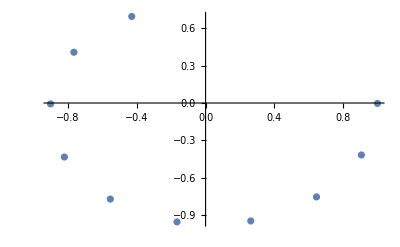

```mathematica
ListPlot[mm]
```

```mathematica
rpo ={} ;
refpower[bbb_] := (
AppendTo[rpo,{frequencies[[bbb]], datax[[bbb]]^2+datax[[bbb+1]]^2}]

);
Array[refpower,Length[frequencies]];
rpo
```

{{30900000,0.9897},{60800000,0.00757411},{90700000,0.825245},{120600000,1.29976},{150500000,0.49728},{180400000,0.170713},{210300000,0.242696},{240200000,0.209534},{270100000,0.204861},{300000000,0.126275}}

```mathematica
□
```

```mathematica
tpo ={} ;
transmitpower[bbb_] := (
AppendTo[tpo,{frequencies[[bbb]], datay[[bbb]]^2+datay[[bbb+1]]^2}]

);
Array[transmitpower,Length[frequencies]];
tpo
```

{{30900000,3.82544×10^-9},{60800000,2.00354×10^-9},{90700000,6.44396×10^-9},{120600000,7.92695×10^-9},{150500000,2.43631×10^-9},{180400000,6.90771×10^-10},{210300000,7.07948×10^-9},{240200000,6.90247×10^-9},{270100000,1.18393×10^-9},{300000000,2.11789×10^-9}}

```mathematica
rph ={} ;
refphase[bbb_] := (
AppendTo[rph,{frequencies[[bbb]], ArcTan[datax[[bbb]],datax[[bbb+1]]]}]

);
Array[refphase,Length[frequencies]];
rph
```

{{30900000,-0.0586389},{60800000,-2.3049},{90700000,-1.64198},{120600000,-2.48947},{150500000,2.94704},{180400000,1.23454},{210300000,0.657175},{240200000,-0.853368},{270100000,-2.43726},{300000000,2.54057}}

```mathematica
tph ={} ;
transmitphase[bbb_] := (
AppendTo[tph,{frequencies[[bbb]], ArcTan[datay[[bbb]],datay[[bbb+1]]]}]

);
Array[transmitphase,Length[frequencies]];
tph
```

{{30900000,-0.693718},{60800000,-2.65411},{90700000,-1.83504},{120600000,-2.62666},{150500000,2.66449},{180400000,0.530808},{210300000,-1.412},{240200000,3.13996},{270100000,-1.56684},{300000000,-2.41534}}